## G=4 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
<<MaTeX`
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
```

### Model 13: PdP_1 = ℂ^3/ℤ_4 (1,1,2)=Y^(2,2)

```mathematica
WPdP1=Sum[LeviCivitaTensor[2]⟦a,b⟧ (Subscript[X, 1][2,4]·Subscript[X, a][4,1]·Subscript[X, b][1,2]+Subscript[X, 1][4,2]·Subscript[X, a][2,3]·Subscript[X, b][3,4]+Subscript[X, 1][1,3]·Subscript[X, a][3,4]·Subscript[X, b][4,1]+Subscript[X, 1][3,1]·Subscript[X, a][1,2]·Subscript[X, b][2,3]),{a,2},{b,2}];
```

```mathematica
PdP1=Model["PdP1","Descriptions"->{"ℂ","PdP","Y"},"Potential"->WPdP1];
```

### Model 14: dP_1

```mathematica
WdP1=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1])+Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 2][4,2]·Subscript[X, 3][2,1]+Subscript[X, 1][3,2]·Subscript[X, 3][2,1]·Subscript[X, 2][1,3]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,2]·Subscript[X, 2][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,2]·Subscript[X, 2][2,1]·Subscript[X, 2][1,3];
```

```mathematica
dP1=Model["dP1","Descriptions"->{"dP"},"Potential"->WdP1];
```

### Model 15: 𝔽_0 = 𝒞/ℤ_2 (1,1,1,1 )

```mathematica
WF0PhaseA=Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 2][3,4]·Subscript[X, 2][4,1]-Subscript[X, 1][1,2]·Subscript[X, 2][2,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,1]·Subscript[X, 2][1,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,1]·Subscript[X, 2][1,2]·Subscript[X, 2][2,3];
```

```mathematica
WF0PhaseB=X[2,1]·X[1,4]·X[4,2]+X[2,1,2]·X[1,4,2]·X[4,2,2]+X[2,3,1]·X[3,4,2]·X[4,2,3]+X[2,3,2]·X[3,4,1]·X[4,2,4]-X[2,1,1]·X[1,4,2]·X[4,2,3]-X[2,1,2]·X[1,4,1]·X[4,2,4]-X[2,3,1]·X[3,4,1]·X[4,2,2]-X[2,3,2]·X[3,4,2]·X[4,2,1];
```

```mathematica
F0PhaseA=Model[{"F0","PhaseA"},"Potential"->WF0PhaseA];
F0PhaseB=Model[{"F0","PhaseB"},"QuiverPositioning"->{{1,3},2,4},"Potential"->WF0PhaseB];
```

## Deformations

### PdP_1 ⟹ 𝔽_0 (a)

#### Deformation 1: (1→3→1) – (2→4→2)

```mathematica
PdP1def1η=Subscript[X, 1][2,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,1]·Subscript[X, 2][1,2];
```

```mathematica
WPdP1def1=WPdP1+μ (Subscript[X, 1][1,3]·Subscript[X, 1][3,1]-Subscript[X, 1][2,4]·Subscript[X, 1][4,2]);
```

```mathematica
WPdP1def1Min=WPdP1def1//IntegrateOutMassTerms
```

1/μ(-(X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1])+X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]+X_1[2,3]·X_1[3,4]·X_2[4,1]·X_2[1,2]-X_1[3,4]·X_1[4,1]·X_2[1,2]·X_2[2,3])

```mathematica
μ (Subscript[X, 1][1,3]·Subscript[X, 1][3,1]-Subscript[X, 1][2,4]·Subscript[X, 1][4,2])/.Echo@Last@Solve[DG[WPdP1def1,{massiveFieldsFrom[WPdP1def1]}]==0,massiveFieldsFrom[WPdP1def1]]//FullSimplify
```

{X_1[1,3]→(-(X_1[1,2]·X_2[2,3])+X_2[1,2]·X_1[2,3])/μ,X_1[2,4]→(X_1[2,3]·X_2[3,4]-X_2[2,3]·X_1[3,4])/μ,X_1[3,1]→(-(X_1[3,4]·X_2[4,1])+X_2[3,4]·X_1[4,1])/μ,X_1[4,2]→(X_1[4,1]·X_2[1,2]-X_2[4,1]·X_1[1,2])/μ}

(X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]-X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]-X_1[2,3]·X_1[3,4]·X_2[4,1]·X_2[1,2]+X_1[3,4]·X_1[4,1]·X_2[1,2]·X_2[2,3])/μ

```mathematica
Clear[RedefChoice1,RedefRules1]
RedefChoice1={};
RedefRules1={Subscript[X, 1][1,2]->μ Subscript[X, 1][1,2],Subscript[X, 2][1,2]->μ Subscript[X, 2][1,2]};
RedefRules1 //Column
```

X_1[1,2]→μ X_1[1,2]
X_2[1,2]→μ X_2[1,2]

```mathematica
WF0AFromDef1=(WPdP1def1Min/.RedefRules1)//Simplify;
```

```mathematica
WF0AFromDef1+1/μ(Total@ZigZagOperator[WF0AFromDef1][PdP1def1η])
```

-(X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1])+X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]+X_1[2,3]·X_1[3,4]·X_2[4,1]·X_2[1,2]-X_1[3,4]·X_1[4,1]·X_2[1,2]·X_2[2,3]

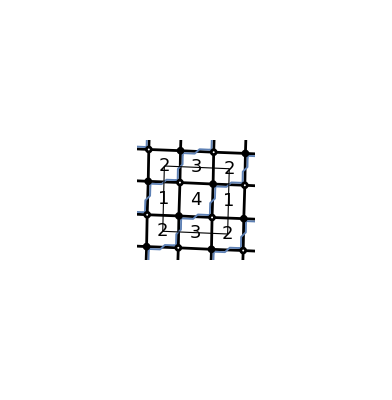

```mathematica
BraneTilingGraph[WF0AFromDef1,"ZigZags"->{PdP1def1η}]
```

```mathematica
(WF0AFromDef1)+λ WF0PhaseA//Collect[Simplify@#,_CenterDot,Highlighted@*Simplify]&
```

X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1] 1-λ+X_1[2,3]·X_1[3,4]·X_2[4,1]·X_2[1,2] 1-λ+X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1] -1+λ+X_1[3,4]·X_1[4,1]·X_2[1,2]·X_2[2,3] -1+λ

## Mesonic branch

### Model 13: PdP_1 = ℂ^3/ℤ_4 (1,1,2)=Y^(2,2)

```mathematica
PdP1FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP1,4];
```

```mathematica
PdP1FieldGenRules0//Column
```

X_1[2,4]·X_1[4,2]→A[1]
X_1[1,3]·X_1[3,1]→A[2]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[1]
X_1[2,3]·X_2[3,4]·X_1[4,2]→B[2]
X_2[2,3]·X_1[3,4]·X_1[4,2]→B[3]
X_2[2,3]·X_2[3,4]·X_1[4,2]→B[4]
X_1[1,3]·X_1[3,4]·X_1[4,1]→B[5]
X_1[1,3]·X_1[3,4]·X_2[4,1]→B[6]
X_1[1,3]·X_2[3,4]·X_1[4,1]→B[7]
X_1[1,3]·X_2[3,4]·X_2[4,1]→B[8]
X_1[1,2]·X_1[2,4]·X_1[4,1]→B[9]
X_1[1,2]·X_1[2,4]·X_2[4,1]→B[10]
X_2[1,2]·X_1[2,4]·X_1[4,1]→B[11]
X_2[1,2]·X_1[2,4]·X_2[4,1]→B[12]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[13]
X_1[1,2]·X_2[2,3]·X_1[3,1]→B[14]
X_2[1,2]·X_1[2,3]·X_1[3,1]→B[15]
X_2[1,2]·X_2[2,3]·X_1[3,1]→B[16]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[1]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→C[2]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→C[3]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[4]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→C[5]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→C[6]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[7]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→C[8]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[9]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→C[10]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→C[11]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[12]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→C[13]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→C[14]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[15]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→C[16]

```mathematica
PdP1FieldGenRules=ReduceGenerators[WPdP1,Keys@PdP1FieldGenRules0,PdP1FieldGenRules0];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
PdP1FieldGenRules//Column
```

X_1[2,4]·X_1[4,2]→A[1]
X_1[1,3]·X_1[3,1]→A[2]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[1]
X_1[2,3]·X_2[3,4]·X_1[4,2]→B[3]
X_2[2,3]·X_1[3,4]·X_1[4,2]→B[3]
X_2[2,3]·X_2[3,4]·X_1[4,2]→B[4]
X_1[1,3]·X_1[3,4]·X_1[4,1]→B[1]
X_1[1,3]·X_1[3,4]·X_2[4,1]→B[3]
X_1[1,3]·X_2[3,4]·X_1[4,1]→B[3]
X_1[1,3]·X_2[3,4]·X_2[4,1]→B[4]
X_1[1,2]·X_1[2,4]·X_1[4,1]→B[1]
X_1[1,2]·X_1[2,4]·X_2[4,1]→B[3]
X_2[1,2]·X_1[2,4]·X_1[4,1]→B[3]
X_2[1,2]·X_1[2,4]·X_2[4,1]→B[4]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[1]
X_1[1,2]·X_2[2,3]·X_1[3,1]→B[3]
X_2[1,2]·X_1[2,3]·X_1[3,1]→B[3]
X_2[1,2]·X_2[2,3]·X_1[3,1]→B[4]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[1]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→C[9]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→C[9]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[13]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→C[9]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→C[13]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[13]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→C[15]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[9]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→C[13]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→C[13]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[15]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→C[13]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→C[15]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[15]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→C[16]

```mathematica
PdP1FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[FTerms@WPdP1==0],Equal@@@PdP1FieldGenRules],FieldCases@WPdP1]
```

-A[1] B[1]+A[2] B[1]==0&&-A[1] B[3]+A[2] B[3]==0&&-A[1] B[4]+A[2] B[4]==0&&-B[3]^2+B[1] B[4]==0&&-B[1]^2+A[1] C[1]==0&&-B[1]^2+A[2] C[1]==0&&-B[1] B[3]+A[1] C[9]==0&&-B[1] B[3]+A[2] C[9]==0&&-B[3] C[1]+B[1] C[9]==0&&B[4] C[1]-B[3] C[9]==0&&-B[3]^2+A[1] C[13]==0&&-B[3]^2+A[2] C[13]==0&&-B[3] C[9]+B[1] C[13]==0&&B[4] C[9]-B[3] C[13]==0&&C[9]^2-C[1] C[13]==0&&-B[3] B[4]+A[1] C[15]==0&&-B[3] B[4]+A[2] C[15]==0&&-B[3] C[13]+B[1] C[15]==0&&B[4] C[13]-B[3] C[15]==0&&-C[9] C[13]+C[1] C[15]==0&&-C[13]^2+C[9] C[15]==0&&-B[4]^2+A[1] C[16]==0&&-B[4]^2+A[2] C[16]==0&&-B[3] C[15]+B[1] C[16]==0&&B[4] C[15]-B[3] C[16]==0&&-C[13]^2+C[1] C[16]==0&&-C[13] C[15]+C[9] C[16]==0&&C[15]^2-C[13] C[16]==0

```mathematica
PdP1FieldMesonicIdeal=First@PrimaryDecompositionM2[PdP1FieldChiralIdeal,UniqueCases[PdP1FieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Solve[#[{1,1}]==0]]&)
```

{A[2]→A[1]}

C[15]^2==C[13] C[16]&&C[13] C[15]==C[9] C[16]&&C[9] C[15]==C[1] C[16]&&B[4] C[15]==B[3] C[16]&&B[3] C[15]==B[1] C[16]&&C[13]^2==C[1] C[16]&&C[9] C[13]==C[1] C[15]&&B[4] C[13]==B[1] C[16]&&B[3] C[13]==B[1] C[15]&&C[9]^2==C[1] C[13]&&B[4] C[9]==B[1] C[15]&&B[3] C[9]==B[1] C[13]&&B[4] C[1]==B[1] C[13]&&B[3] C[1]==B[1] C[9]&&B[4]^2==A[1] C[16]&&B[3] B[4]==A[1] C[15]&&B[1] B[4]==A[1] C[13]&&B[3]^2==A[1] C[13]&&B[1] B[3]==A[1] C[9]&&B[1]^2==A[1] C[1]

```mathematica
PdP2GenSU2Relabel={A[1]->A[0],B[1]->B[-2],B[3]->B[0],B[4]->B[2],C[1]->B[-4],C[9]->C[-2],C[13]->C[0],C[15]->C[2],C[16]->C[4]};
```

```mathematica
PdP1FieldMesonicIdeal/.PdP2GenSU2Relabel
```

C[2]^2==C[0] C[4]&&C[0] C[2]==C[-2] C[4]&&C[-2] C[2]==B[-4] C[4]&&B[2] C[2]==B[0] C[4]&&B[0] C[2]==B[-2] C[4]&&C[0]^2==B[-4] C[4]&&C[-2] C[0]==B[-4] C[2]&&B[2] C[0]==B[-2] C[4]&&B[0] C[0]==B[-2] C[2]&&C[-2]^2==B[-4] C[0]&&B[2] C[-2]==B[-2] C[2]&&B[0] C[-2]==B[-2] C[0]&&B[-4] B[2]==B[-2] C[0]&&B[-4] B[0]==B[-2] C[-2]&&B[2]^2==A[0] C[4]&&B[0] B[2]==A[0] C[2]&&B[-2] B[2]==A[0] C[0]&&B[0]^2==A[0] C[0]&&B[-2] B[0]==A[0] C[-2]&&B[-2]^2==A[0] B[-4]

### Model 14: dP_1

```mathematica
dP1FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WdP1,4];
```

```mathematica
dP1FieldGenRules=ReduceGenerators[WdP1,Keys@dP1FieldGenRules0,dP1FieldGenRules0];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
dP1FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[FTerms@WdP1==0],Equal@@@dP1FieldGenRules],FieldCases@WdP1]
```

B[3] B[5]-B[2] B[6]==0&&B[2] B[4]-B[5] B[6]==0&&B[3] B[4]-B[6]^2==0&&-B[3]^2+B[2] C[3]==0&&-B[3] B[6]+B[5] C[3]==0&&-B[3] B[6]+B[2] C[9]==0&&-B[6] C[3]+B[3] C[9]==0&&-B[6]^2+B[5] C[9]==0&&B[4] C[3]-B[6] C[9]==0&&-B[4] B[6]+B[2] C[10]==0&&-B[4]^2+B[5] C[10]==0&&-B[6]^2+B[2] C[12]==0&&-B[6] C[9]+B[3] C[12]==0&&-B[6] C[10]+B[4] C[12]==0&&-B[4] B[6]+B[5] C[12]==0&&B[4] C[9]-B[6] C[12]==0&&B[3] C[10]-B[6] C[12]==0&&C[9]^2-C[3] C[12]==0&&C[3] C[10]-C[9] C[12]==0&&C[9] C[10]-C[12]^2==0

```mathematica
dP1FieldMesonicIdeal=First@PrimaryDecompositionM2[dP1FieldChiralIdeal,UniqueCases[dP1FieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Solve[#[{1,1}]==0]]&)
```

{}

C[9] C[10]==C[12]^2&&C[3] C[10]==C[9] C[12]&&B[6] C[10]==B[4] C[12]&&B[2] C[10]==B[5] C[12]&&B[3] C[10]==B[6] C[12]&&C[9]^2==C[3] C[12]&&B[4] C[9]==B[6] C[12]&&B[6] C[9]==B[3] C[12]&&B[5] C[9]==B[2] C[12]&&B[4] C[3]==B[3] C[12]&&B[6] C[3]==B[3] C[9]&&B[5] C[3]==B[2] C[9]&&B[4]^2==B[5] C[10]&&B[4] B[6]==B[5] C[12]&&B[3] B[4]==B[2] C[12]&&B[6]^2==B[2] C[12]&&B[2] B[4]==B[5] B[6]&&B[3] B[6]==B[2] C[9]&&B[3] B[5]==B[2] B[6]&&B[3]^2==B[2] C[3]

### Model 15: 𝔽_0 = 𝒞/ℤ_2 (1,1,1,1 )

```mathematica
F0FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WF0PhaseA,4];
```

```mathematica
F0FieldGenRules=ReduceGenerators[WF0PhaseA,Keys@F0FieldGenRules0,F0FieldGenRules0];
```

Abelianize::warn: Abelianization of the fields was done.

```mathematica
F0FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[FTerms@WF0PhaseA==0],Equal@@@F0FieldGenRules],FieldCases@WF0PhaseA]
```

-C[5]^2+C[1] C[6]==0&&-C[9]^2+C[1] C[11]==0&&C[5] C[9]-C[1] C[13]==0&&C[6] C[9]-C[5] C[13]==0&&C[5] C[11]-C[9] C[13]==0&&C[6] C[11]-C[13]^2==0&&-C[5] C[13]+C[1] C[14]==0&&-C[6] C[13]+C[5] C[14]==0&&-C[13]^2+C[9] C[14]==0&&-C[9] C[13]+C[1] C[15]==0&&-C[13]^2+C[5] C[15]==0&&-C[13] C[14]+C[6] C[15]==0&&-C[11] C[13]+C[9] C[15]==0&&C[11] C[14]-C[13] C[15]==0&&-C[13]^2+C[1] C[16]==0&&-C[13] C[14]+C[5] C[16]==0&&-C[14]^2+C[6] C[16]==0&&-C[13] C[15]+C[9] C[16]==0&&-C[15]^2+C[11] C[16]==0&&C[14] C[15]-C[13] C[16]==0

```mathematica
F0FieldMesonicIdeal=First@PrimaryDecompositionM2[F0FieldChiralIdeal,UniqueCases[F0FieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Solve[#[{1,1}]==0]]&)
```

{}

C[15]^2==C[11] C[16]&&C[14] C[15]==C[13] C[16]&&C[13] C[15]==C[9] C[16]&&C[6] C[15]==C[5] C[16]&&C[5] C[15]==C[1] C[16]&&C[14]^2==C[6] C[16]&&C[13] C[14]==C[5] C[16]&&C[11] C[14]==C[9] C[16]&&C[9] C[14]==C[1] C[16]&&C[13]^2==C[1] C[16]&&C[11] C[13]==C[9] C[15]&&C[9] C[13]==C[1] C[15]&&C[6] C[13]==C[5] C[14]&&C[5] C[13]==C[1] C[14]&&C[6] C[11]==C[1] C[16]&&C[5] C[11]==C[1] C[15]&&C[9]^2==C[1] C[11]&&C[6] C[9]==C[1] C[14]&&C[5] C[9]==C[1] C[13]&&C[5]^2==C[1] C[6]

### PdP_1 ⟹ 𝔽_0 (a)

#### Deformation 1: (1→3→1) – (2→4→2)

```mathematica
PdP1DefFieldGenRules0=GroupBy[PdP1FieldGenRules/.PdP2GenSU2Relabel,Last->First]//KeyValueMap[Thread[#2->ReplaceAll[(x:$GeneratorVars)[s_]:>(x[s,#]&/@Range@Length[#2])]@#1]&]//Flatten;
```

```mathematica
PdP1DefFieldGenRules=ReduceGenerators[WPdP1def1,Keys@PdP1DefFieldGenRules0,PdP1DefFieldGenRules0,"RemoveDenominators"->True];
PdP1DefFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[2,4]·X_1[4,2]→A[0,1]
X_1[1,3]·X_1[3,1]→A[0,1]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[-2,1]
X_1[1,3]·X_1[3,4]·X_1[4,1]→B[-2,1]
X_1[1,2]·X_1[2,4]·X_1[4,1]→B[-2,1]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[-2,1]
X_1[2,3]·X_2[3,4]·X_1[4,2]→μ A[0,1]+B[0,2]
X_2[2,3]·X_1[3,4]·X_1[4,2]→B[0,2]
X_1[1,3]·X_1[3,4]·X_2[4,1]→B[0,2]
X_1[1,3]·X_2[3,4]·X_1[4,1]→μ A[0,1]+B[0,2]
X_1[1,2]·X_1[2,4]·X_2[4,1]→B[0,2]
X_2[1,2]·X_1[2,4]·X_1[4,1]→μ A[0,1]+B[0,2]
X_1[1,2]·X_2[2,3]·X_1[3,1]→B[0,2]
X_2[1,2]·X_1[2,3]·X_1[3,1]→μ A[0,1]+B[0,2]
X_2[2,3]·X_2[3,4]·X_1[4,2]→B[2,1]
X_1[1,3]·X_2[3,4]·X_2[4,1]→B[2,1]
X_2[1,2]·X_1[2,4]·X_2[4,1]→B[2,1]
X_2[1,2]·X_2[2,3]·X_1[3,1]→B[2,1]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→B[-4,1]
X_1[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→-μ B[-2,1]+C[-2,4]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→C[-2,4]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→-μ B[-2,1]+C[-2,4]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_1[4,1]→C[-2,4]
X_1[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[0,6]
X_1[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→-μ B[0,2]+C[0,6]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[0,6]
X_2[1,2]·X_1[2,3]·X_1[3,4]·X_2[4,1]→C[0,6]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_1[4,1]→μ^2 A[0,1]+μ B[0,2]+C[0,6]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_1[4,1]→C[0,6]
X_1[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→-μ B[2,1]+C[2,4]
X_2[1,2]·X_1[2,3]·X_2[3,4]·X_2[4,1]→C[2,4]
X_2[1,2]·X_2[2,3]·X_1[3,4]·X_2[4,1]→-μ B[2,1]+C[2,4]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_1[4,1]→C[2,4]
X_2[1,2]·X_2[2,3]·X_2[3,4]·X_2[4,1]→C[4,1]

```mathematica
PdP1DefFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP1def1],Equal@@@PdP1DefFieldGenRules],FieldCases@WPdP1def1];
```

```mathematica
PdP1DefFieldChiralIdealFinal=ReplaceAll[Subscript[X, a_][1,2]·Subscript[X, b_][2,3]·Subscript[X, c_][3,4]·Subscript[X, d_][4,1]:>Y[-6+2(a+c),-6+2(b+d)]]@Select[PdP1DefFieldGenRules,Count[First@#,Subscript[X, _][__]]==4&]//Join[Equal@@@#,List@@PdP1DefFieldChiralIdeal]&//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&;
```

```mathematica
solY=ReplaceAll[Subscript[X, a_][1,2]·Subscript[X, b_][2,3]·Subscript[X, c_][3,4]·Subscript[X, d_][4,1]:>Y[-6+2(a+c),-6+2(b+d)]]@Select[Equal@@@PdP1DefFieldGenRules,Count[First@#,Subscript[X, _][__]]==4&]//First@Solve[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&
```

{A[0,1]→-(-Y[-2,2]+2 Y[0,0]-Y[2,-2])/μ^2,B[-4,1]→Y[-2,-2],B[-2,1]→-(Y[-2,0]-Y[0,-2])/μ,B[0,2]→-(Y[-2,2]-Y[0,0])/μ,B[2,1]→-(Y[0,2]-Y[2,0])/μ,C[-2,4]→Y[0,-2],C[0,6]→Y[0,0],C[2,4]→Y[2,0],C[4,1]→Y[2,2]}

```mathematica
F0FieldChiralIdeal/.ReplaceAll[Subscript[X, a_][1,2]·Subscript[X, b_][2,3]·Subscript[X, c_][3,4]·Subscript[X, d_][4,1]:>Y[-6+2(a+c),-6+2(b+d)]]@Select[Reverse/@F0FieldGenRules,Count[Last@#,Subscript[X, _][__]]==4&]//Simplify//Sort//Map[Sort]//{List@@PdP1DefFieldChiralIdealFinal//GroebnerBasis,#//GroebnerBasis}&//Map@Column
```

{-Y[2,0]^2+Y[2,-2] Y[2,2]
-Y[0,2] Y[2,0]+Y[0,0] Y[2,2]
-Y[0,2] Y[2,-2]+Y[0,0] Y[2,0]
-Y[0,2] Y[2,-2]+Y[0,-2] Y[2,2]
-Y[0,0] Y[2,-2]+Y[0,-2] Y[2,0]
-Y[0,0]^2+Y[0,-2] Y[0,2]
-Y[0,2]^2+Y[-2,2] Y[2,2]
-Y[0,0] Y[0,2]+Y[-2,2] Y[2,0]
-Y[0,0]^2+Y[-2,2] Y[2,-2]
-Y[0,0]^2+Y[-2,-2] Y[2,2]
-Y[0,-2] Y[0,0]+Y[-2,-2] Y[2,0]
-Y[0,-2]^2+Y[-2,-2] Y[2,-2]
-Y[-2,2] Y[0,-2]+Y[-2,-2] Y[0,2]
-Y[-2,2] Y[0,-2]^2+Y[-2,-2] Y[0,0]^2
-Y[0,0] Y[0,2]+Y[-2,0] Y[2,2]
-Y[0,0]^2+Y[-2,0] Y[2,0]
-Y[0,-2] Y[0,0]+Y[-2,0] Y[2,-2]
-Y[-2,2] Y[0,0]+Y[-2,0] Y[0,2]
-Y[-2,2] Y[0,-2]+Y[-2,0] Y[0,0]
Y[-2,0] Y[0,-2]-Y[-2,-2] Y[0,0]
Y[-2,0]^2-Y[-2,-2] Y[-2,2],-Y[2,0]^2+Y[2,-2] Y[2,2]
-Y[0,2] Y[2,0]+Y[0,0] Y[2,2]
-Y[0,2] Y[2,-2]+Y[0,0] Y[2,0]
-Y[0,2] Y[2,-2]+Y[0,-2] Y[2,2]
-Y[0,0] Y[2,-2]+Y[0,-2] Y[2,0]
-Y[0,0]^2+Y[0,-2] Y[0,2]
-Y[0,2]^2+Y[-2,2] Y[2,2]
-Y[0,0] Y[0,2]+Y[-2,2] Y[2,0]
-Y[0,0]^2+Y[-2,2] Y[2,-2]
-Y[0,0]^2+Y[-2,-2] Y[2,2]
-Y[0,-2] Y[0,0]+Y[-2,-2] Y[2,0]
-Y[-2,2] Y[0,-2]+Y[-2,-2] Y[0,2]
-Y[0,-2]^2+Y[-2,-2] Y[2,-2]
-Y[-2,2] Y[0,-2]^2+Y[-2,-2] Y[0,0]^2
-Y[0,0] Y[0,2]+Y[-2,0] Y[2,2]
-Y[0,0]^2+Y[-2,0] Y[2,0]
-Y[-2,2] Y[0,0]+Y[-2,0] Y[0,2]
-Y[0,-2] Y[0,0]+Y[-2,0] Y[2,-2]
-Y[-2,2] Y[0,-2]+Y[-2,0] Y[0,0]
Y[-2,0] Y[0,-2]-Y[-2,-2] Y[0,0]
Y[-2,0]^2-Y[-2,-2] Y[-2,2]}

## Resolutions flow

### PdP_1 ⟹ 𝔽_0 (a)

#### Deformation 1: (1→3→1) – (2→4→2)

```mathematica
kcCompTbPdP1=KahlerChambersCompatibility[WPdP1,"ShowProgress"->True];
kcCompTbF0A=KahlerChambersCompatibility[WF0AFromDef1,"ShowProgress"->True];
```

```mathematica
kcFlowPdP1F0A=KahlerChambersFlowGraph[kcCompTbPdP1,kcCompTbF0A,"ShowProgress"->True];
```

## Resolutions volumes

### PdP_1 ⟹ 𝔽_0 (a)

#### Deformation 1: (1→3→1) – (2→4→2)

```mathematica
kvTablePdP1=KahlerVolumes[WPdP1,"ShowProgress"->True];
kvTableF0A=KahlerVolumes[WF0AFromDef1,"ShowProgress"->True];
```

```mathematica
tM={{1,1},{0,1}};
polytVolPdP1F0A=volumesTable[
MapAt[KeyMap[x↦tM.x],{All,-1,2}]@MapAt[TransformedMesh[tM],{All,-1,1}]@Map[SortBy@First]@WeaklyConnectedComponents[kcFlowPdP1F0A],
{kvTablePdP1,Map[
KeyMap[KeyMap[x↦tM.x]]@*Map[KeyMap[x↦x.Transpose[tM]]],
KeyMap[TransformedMesh[tM]]@kvTableF0A]}
]
```

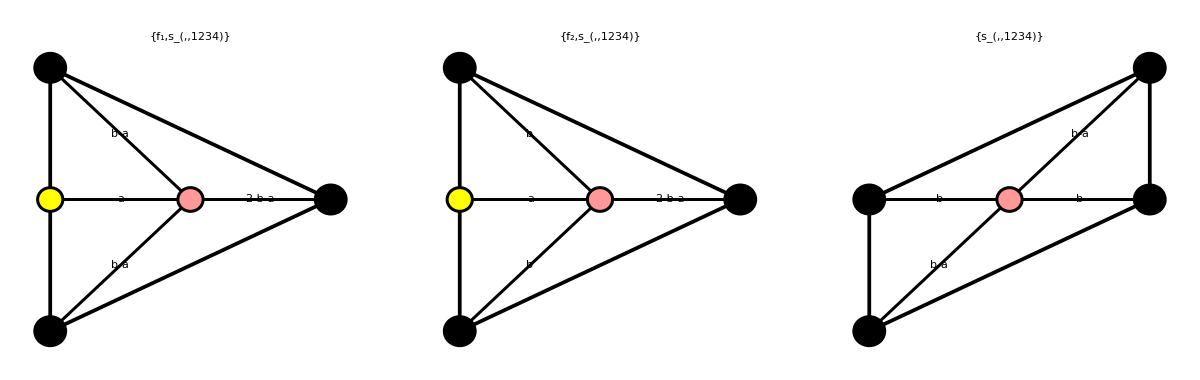

```mathematica
KeyValueMap[
{k,v}↦MapThread[PolytopePlot[#1,"PolytopeCellLabel"->Normal[(Style[#,Background->LightBlue]&)/@#2],PlotLabel->#3]&,{Splice@Transpose@k,First@v}],
polytVolPdP1F0A
]//ReverseSortBy[Length]//Map[GraphicsRow]//Column
```